```mathematica
Integrate[1/(2 u)*h^(-3/2), {h, u, 1}, Assumptions->0<u≤h<1]
```

1/u^(3/2)-1/u

```mathematica
delta[p_]:=2 p/(1 - p);
delta[p]
```

(2 p)/(1-p)

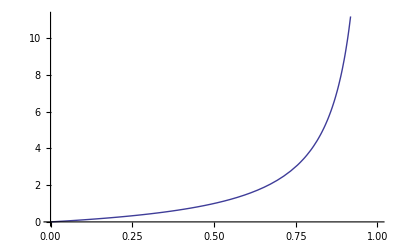

```mathematica
Plot[p/(1-p),{p,0,1}]
```

```mathematica
Reduce[p/(1-p) ≤1 && p>0&&p<1]
```

0<p≤1/2

```mathematica
g[y_]:=(1-p)/(1-y)^(1/2);
randomize2 = Integrate[g[y], {y, 0, 1-(1-p)^2}, Assumptions->0<p<1]
```

-2 (-1+p) p

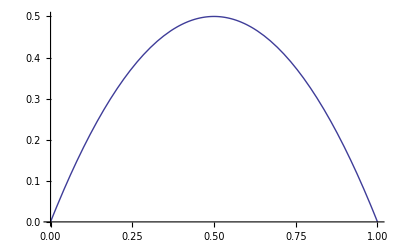

```mathematica
Plot[-2 (-1+p) p,{p,0,1}]
```

```mathematica
ga[u_,c_]:=c* u^(-3/2);
Simplify[Integrate[ga[u,c], {u, p^2, 1}], Assumptions->0<p<1]
```

```mathematica
-(2 c (-1+p))/p/.c-> (Sqrt[p^2 + 4*p/(1-p)]-p)/(4*(1-p))
```

-((-1+p) (-p+√((4 p)/(1-p)+p^2)))/(2 (1-p) p)

```mathematica
Simplify[-((-1+p) (-p+√((4 p)/(1-p)+p^2)))/(2 (1-p) p), Assumptions->0<p<1]
```

```mathematica
theconst=1/2 (-1+√((4+p-p^2)/(p-p^2)));
```

```mathematica
c = FullSimplify[p*theconst/(2*(1-p)), Assumptions->0<p<1]
delta = FullSimplify[1/(1 + theconst), Assumptions->0<p<1]
gcoeff = FullSimplify[delta*c, Assumptions->0<p<1]
densityPart = FullSimplify[Integrate[ga[u, gcoeff], {u, p^2, 1}], Assumptions->0<p<1];
Simplify[densityPart + delta, Assumptions->0<p<1];
```

(p-√(p (-4/(-1+p)+p)))/(4 (-1+p))

2/(1+√(1-4/(-1+p)+4/p))

(p-√(p (-4/(-1+p)+p)))/(2 (1+√(1-4/(-1+p)+4/p)) (-1+p))

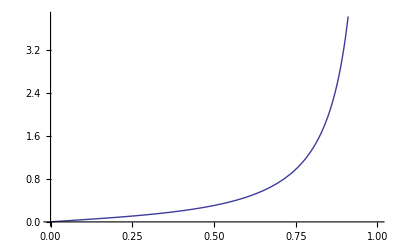

```mathematica
Plot[(p-√(p (-4/(-1+p)+p)))/(2 (1+√(1-4/(-1+p)+4/p)) (-1+p)),{p,0,1}]
```

```mathematica
l[ksi_, eta_]:=(1-p)*ksi-p*eta+p
l1[ksi_] := l[ksi, 1]
l1[ksi]
density[ksi_]:=p/(2*(1-p))*ksi^(-3/2)
density[ksi]
FullSimplify[Integrate[l1[ksi]*density[ksi], {ksi, p^2, 1}], Assumptions->0<p<1]
```

ksi (1-p)

p/(2 ksi^(3/2) (1-p))

-(-1+p) p